-Graphics-

Podpořeno z projektu OPEN UNI - zlepšení otevřenosti a atraktivnosti studia na SU, CZ .02 .2 .69/0.0/0.0/18 _ 056/0013364.

# The surface of a torus in the vicinity of a neutron star

## The geometry

To describe the spacetime around a neutron star we use the Hartle-Thorne metric (Hartle, J. B. & Thorne, K. S. 1968, APJ, 153, 807). 
For the calculation we use relations derived by Abramowicz, M . A ., Almergren, G . J . E ., Kluźniak, W ., & Thampan, A . V . 2003, gr qc, gr - qc/0312070.

### The Hartle-Thorne metric coefficients

```mathematica
M=1;

F1=-(8M r^4 (r-2M))^(-1)(u^2(48M^6-8M^5r-24M^4r^2-30M^3r^3-60M^2r^4+135M r^5-45r^6)+(r-M)(16M^5+8M^4r-10M^2r^3-30M r^4+15r^5))+A1;
F2=(8M r(r-2M))^(-1)5(3u^2-1)(r-M)(2M^2+6M r-3r^2)-A1;
G1=(8M r^4 (r-2M))^(-1)(L-72M^5r-3u^2(L-56M^5r))-A1;
L=80M^6+8M^4r^2+10M^3r^3+20M^2r^4-45M r^5+15r^6;
H1=(8M r^4)^(-1)(1-3u^2)(16M^5+8M^4r-10M^2r^3+15M r^4+15r^5)+A2;
H2=(8M r)^(-1)5(1-3u^2)(2M^2-3M r-3r^2)-A2;
A1=15r(r-2M)(1-3u^2)/(16M^2) Log[r/(r-2M)];
A2 =15(r^2-2M^2)(3u^2-1)/(16M^2) Log[r/(r-2M)];
u = Cos[h];

metric=Array[g,{4,4}];
g[1,1]=-(1-2M/r)(1+j^2F1+q F2); g[1,2]=0; g[1,3]=0; g[1,4]=-2M^2/r j  (1-u^2);
g[2,1]=0; g[2,2]=(1-2M/r)^(-1)(1+j^2G1-q F2); g[2,3]=0; g[2,4]=0;
g[3,1]=0; g[3,2]=0; g[3,3]=r^2(1+j^2H1+q H2); g[3,4]=0;
g[4,1]=g[1,4]; g[4,2]=0; g[4,3]=0; g[4,4]=r^2(1-u^2)(1+j^2H1+q H2);

inversemetric=Inverse[metric];

gtt=Simplify[metric[[1,1]]];
gtp=Simplify[metric[[1,4]]];
grr=Simplify[metric[[2,2]]];
ghh=Simplify[metric[[3,3]]];
gpp=Simplify[metric[[4,4]]];

gTT=Simplify[inversemetric[[1,1]]]; 
gTP=Simplify[inversemetric[[1,4]]];
gRR=Simplify[inversemetric[[2,2]]];
gHH=Simplify[inversemetric[[3,3]]];
gPP=Simplify[inversemetric[[4,4]]];
```

### The orbital angular velocity

```mathematica
F1om=(48M^7-80M^6r+4M^5r^2-18M^4r^3+40M^3r^4+10M^2r^5+15M r^6-15r^7)(16M^2r^4(r-2M))^(-1)+Aom;
F2om=(5(6M^4-8M^3r-2M^2r^2-3M r^3+3r^4)/(16M^2r(r-2M)))-Aom;
Aom=(15(r^3-2M^3)/(32M^3))Log[r/(r-2M)];
Ω=(M^(1/2)/r^(3/2))(1-j(M^(3/2)/r^(3/2))+j^2 F1om+q F2om);
Ω0=Ω/.{r->r0};
Ωlkonst=-(gtp + l0 gtt)/(gpp + l0 gtp);
```

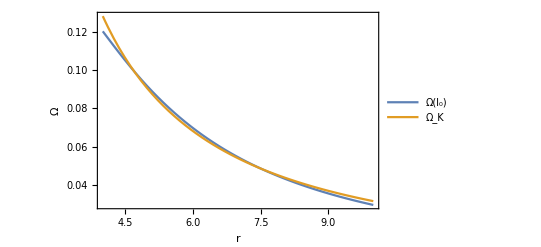

```mathematica
j=0.3;q=8j^2;h=Pi/2;r0=7.5;om1=Ωlkonst;om2=Ω;Clear[j,q,h,r0]; Plot[{om1,om2},{r,4,10},Frame->True,Axes->False,FrameLabel->{"r","Ω"},LabelStyle->Directive[20,FontFamily->"Times New Roman"],PlotLegends->{Row[{"Ω(",Subscript["l","0"],")"}],Subscript["Ω","K"]}]
```

### The time component of the 4-velocity

```mathematica
A =(1/Sqrt[(-gtt-2 Ω gtp-Ω^2 gpp)]);
A0=A/.{r-> r0,h->  π/2};
```

### The specific angular momentum

```mathematica
l = -(gpp *Ω + gtp)/(gtt + gtp*Ω);
l0 = l/.{r-> r0,h-> π/2};
```

```mathematica
L0L=(M^(1/2)r^(3/2))/(r-2M);
F1L=(16M^2r^4(r-2M)^2)^(-1)(96M^8-112M^7r-8M^6r^2-48M^5r^3+42M^4r^4+220M^3r^5-260M^2r^6+105M r^7-15r^8)+AL;
F2L=(16M^2r(r-2M))^(-1)5(6M^4-22M^2r^2+15M r^3-3r^4)+AL;
AL=((15)/(32M^3))(2M^3+4M^2r-4M r^2+r^3)Log[r/(r-2M)];
linl=L0L(1-j((M^(3/2)(3r-4M))/(r^(3/2)(r-2M)))+j^2  F1L-q F2L);
linl0 = linl/.{r-> r0,h-> π/2};
```

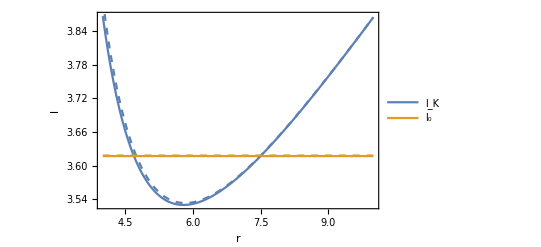

```mathematica
j=0.3;q=8j^2;h=Pi/2;r0=7.5;el=l;el0=l0;linel=linl;linel0=linl0;Clear[j,q,h,r0]; Show[Plot[{el,el0},{r,4,10},Frame->True,Axes->False,FrameLabel->{"r","l"},PlotLegends->{Subscript["l","K"],Subscript["l","0"]},LabelStyle->Directive[20,FontFamily->"Times New Roman"]],Plot[{linel,linel0},{r,4,10},PlotStyle->Dashed]]
```

### The specific energy

```mathematica
ut = -1/Sqrt[(-gTT+2 l0 gTP-l0^2 gPP)]; 
ut0=ut/.{r-> r0, h-> π/2};
```

### The epicyclic frequencies

#### The radial epicyclic frequency

```mathematica
F1r=((6M^(3/2)(r+2M))/(r^(3/2)(r-6M)));
F2r=(8M^2r^4(r-2M)(r-6M))^(-1)(384M^8-720M^7r-112M^6r^2-76M^5r^3-138M^4r^4-130M^3r^5+635M^2r^6-375M r^7+60r^8)+Ar;
F3r=((5(48M^5+30M^4r+26M^3r^2-127M^2r^3+75M r^4-12r^5))/(8M^2r(r-2M)(r-6M)))-Ar;
Ar=((15r(r-2M)(2M^2+13M r-4r^2))/(16M^3(r-6M)))Log[r/(r-2M)];
rad=Sqrt[M(r-6M)r^(-4)(1+j F1r-j^2 F2r -q F3r)];
```

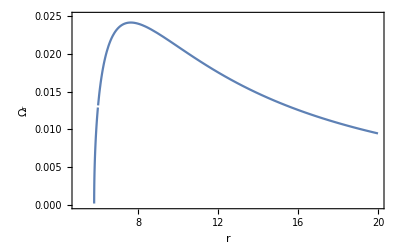

```mathematica
j=0.3;q=8j^2;Plot[rad,{r,5,20},PlotRange->{{5,20},{0,0.025}},Frame->True,Axes->False,FrameLabel->{"r",Subscript["Ω","r"]},LabelStyle->Directive[20,FontFamily->"Times New Roman"]]
Clear[j,q]
```

#### The vertical epicyclic frequency

```mathematica
G1v=6M^(3/2)/r^(3/2);
G2v=(8M^2r^4(r-2M))^(-1)(48M^7-224M^6r+28M^5r^2+6M^4r^3-170M^3r^4+295M^2r^5-165M r^6+30r^7)-Bv;
G3v=((5(6M^4+34M^3r-59M^2r^2+33M r^3-6r^4))/(8M^2r(r-2M)))+Bv;
Bv=((15(2r-M)(r-2M)^2)/16M^3)Log[r/(r-2M)];
vert=Sqrt[M r^(-3)(1-j G1v+j^2 G2v +q G3v)];
```

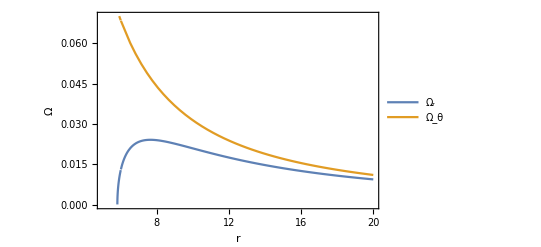

```mathematica
j=0.3;q=8j^2;Plot[{rad,vert},{r,5,20},PlotRange->{{5,20},{0,0.07}},Frame->True,Axes->False,FrameLabel->{"r","Ω"},LabelStyle->Directive[20,FontFamily->"Times New Roman"],PlotLegends->{Subscript["Ω","r"],Subscript["Ω","θ"]}]
Clear[j,q]
```

### Some interesting orbits

#### The innermost stable circular orbit

```mathematica
rms=6M(1-j((2/3)Sqrt[2/3])+j^2((251647/2592)-240Log[3/2])+q((-9325/96)+240Log[3/2]));
```

```mathematica
numrms:=If[j≥0, ftest[r_]=rad^2; count=0; countvalve=100; epsilon=0.000001; a=3M; b=a+5M;  d=0.5(a+b); While[Abs[Chop[ftest[d]]]>epsilon,  count=count+1; d=0.5(a+b); If[Chop[ftest[d]]*Chop[ftest[a]]<0,b=d,a=d]; If[count>countvalve,{Print["error"],Break[]}]];  nrms=d; Clear[a,b,d,ftest,count]; nrms]
```

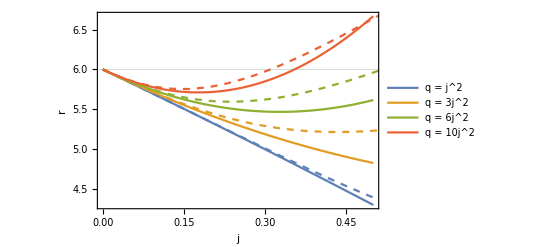

```mathematica
q=j^2; orbit1=Table[{j,numrms},{j,0,0.7,0.01}];  q=3j^2; orbit2=Table[{j,numrms},{j,0,0.7,0.01}]; q=6j^2; orbit3=Table[{j,numrms},{j,0,0.7,0.01}];  q=10j^2; orbit4=Table[{j,numrms},{j,0,0.7,0.01}]; Clear[j,q];
Show[Plot[{rms/.q->1j^2,rms/.q->3j^2,rms/.q->6j^2,rms/.q->10j^2},{j,0,0.5},PlotStyle->{Line},LabelStyle->Directive[20,FontFamily->"Times New Roman"],GridLines->{None,{6}},Frame->True,Axes->False,FrameLabel->{"j","r"},PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"}],ListLinePlot[{orbit1,orbit2,orbit3,orbit4},PlotStyle->{Dashed}]]
```

#### Marginally bound circular orbit

```mathematica
rmb=4M(1-j(1/2)-j^2((8047/256)-45Log[2])+q((1005/32)-45Log[2]));
```

```mathematica
numrmb:=If[j≥0, ftest[r0_]=ut0+1; count=0; countvalve=100; epsilon=0.00001; a=rmb-0.45M; b=7;  d=0.5(a+b); While[Abs[Chop[ftest[d]]]>epsilon,  count=count+1; d=0.5(a+b); If[Chop[ftest[d]]*Chop[ftest[a]]<0,b=d,a=d]; If[count>countvalve,{Print["error"],Break[]}]];  nrmb=d; Clear[a,b,d,ftest,count]; nrmb]
```

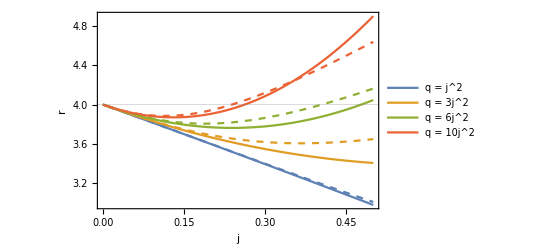

```mathematica
q=j^2; orbit1=Table[{j,numrmb},{j,0.01,0.5,0.01}];  q=3j^2; orbit2=Table[{j,numrmb},{j,0.01,0.5,0.01}]; q=6j^2; orbit3=Table[{j,numrmb},{j,0.01,0.5,0.01}];  q=10j^2; orbit4=Table[{j,numrmb},{j,0.01,0.5,0.01}]; Clear[j,q];
Show[Plot[{rmb/.q->1j^2,rmb/.q->3j^2,rmb/.q->6j^2,rmb/.q->10j^2},{j,0,0.5},PlotStyle->{Line},GridLines->{None,{4}},Frame->True,Axes->False,FrameLabel->{"j","r"},LabelStyle->Directive[20,FontFamily->"Times New Roman"],PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"}],ListLinePlot[{orbit1,orbit2,orbit3,orbit4},PlotStyle->{Dashed}]]
```

#### Frequency resonance

```mathematica
rrez:=If[j≥0, ftest[r_]=Ω/rad-3/2; count=0; countvalve=1000; epsilon=0.000001; a=rms+0.5M; b=20M;  d=0.5(a+b); 
While[Abs[Chop[ftest[d]]]>epsilon,  count=count+1; d=0.5(a+b); If[Chop[ftest[d]]*Chop[ftest[a]]<0,b=d,a=d]; If[count>countvalve,{Print["error"],Break[]}]];  r32=d; Clear[a,b,d,ftest,count]; r32]
```

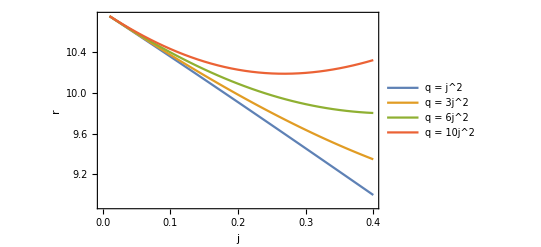

```mathematica
q=j^2; orbit1=Table[{j,rrez},{j,0.01,0.4,0.01}];  q=3j^2; orbit2=Table[{j,rrez},{j,0.01,0.4,0.01}]; q=6j^2; orbit3=Table[{j,rrez},{j,0.01,0.4,0.01}];  q=10j^2; orbit4=Table[{j,rrez},{j,0.01,0.4,0.01}]; Clear[j,q];
ListLinePlot[{orbit1,orbit2,orbit3,orbit4},Frame->True,Axes->False,FrameLabel->{"j","r"},PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"},LabelStyle->Directive[20,FontFamily->"Times New Roman"]]
```

#### Maximum of radial frequency

```mathematica
drad=FullSimplify[D[rad,r]];
rradmax:=If[j≥0, ftest[r_]=drad; count=0; countvalve=1000; epsilon=0.000001; a=rms+0.5M; b=20M;  d=0.5(a+b); 
While[Abs[Chop[ftest[d]]]>epsilon,  count=count+1; d=0.5(a+b); If[Chop[ftest[d]]*Chop[ftest[a]]<0,b=d,a=d]; If[count>countvalve,{Print["error"],Break[]}]];  maxrad=d; Clear[a,b,d,ftest,count]; maxrad]
```

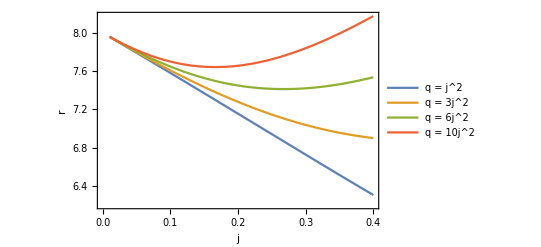

```mathematica
q=j^2; orbit1=Table[{j,rradmax},{j,0.01,0.4,0.01}];  q=3j^2; orbit2=Table[{j,rradmax},{j,0.01,0.4,0.01}]; q=6j^2; orbit3=Table[{j,rradmax},{j,0.01,0.4,0.01}];  q=10j^2; orbit4=Table[{j,rradmax},{j,0.01,0.4,0.01}]; Clear[j,q];
ListLinePlot[{orbit1,orbit2,orbit3,orbit4},Frame->True,Axes->False,FrameLabel->{"j","r"},PlotLegends->{"q = j^2","q = 3j^2","q = 6j^2","q = 10j^2"},LabelStyle->Directive[20,FontFamily->"Times New Roman"]]
```

#### Infinite torus

```mathematica
rmax:=If[j≥0, ftest[r0_]=linl-linl0/.{r->rmb,h->Pi/2}; count=0; countvalve=100; epsilon=0.000001; a=rms; b=20M;  d=0.5(a+b); 
While[Abs[Chop[ftest[d]]]>epsilon,  count=count+1; d=0.5(a+b); If[Chop[ftest[d]]*Chop[ftest[a]]<0,b=d,a=d]; If[count>countvalve,{Print["error"],Break[]}]];  maxr=d; Clear[a,b,d,ftest,count]; maxr]
```

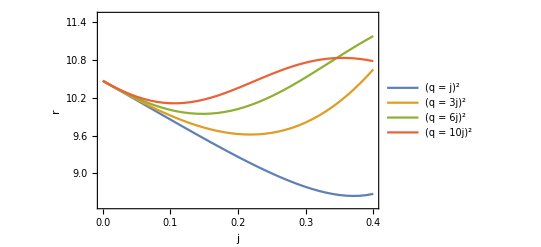

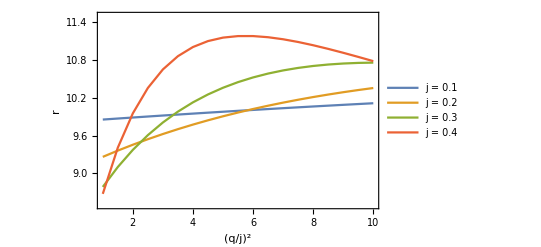

```mathematica
q=x j^2;rmaxtabj=Table[{j,rmax},{x,{1,3,6,10}},{j,0.0,0.4,0.01}]; q=x j^2;rmaxtabq=Table[{x,rmax},{j,0.1,0.4,0.1},{x,1,10,0.5}]; Clear[j,q]
ListLinePlot[rmaxtabj,Frame->True,PlotRange->{{0.0,0.4},{8.5,11.5}},PlotLegends->{Superscript["q = j",2],Superscript["q = 3j",2],Superscript["q = 6j",2],Superscript["q = 10j",2]},FrameLabel->{"j","r"},LabelStyle->Directive[20,FontFamily->"Times New Roman"]]
ListLinePlot[rmaxtabq,Frame->True,PlotRange->{{1,10},{8.5,11.5}},PlotLegends->{"j = 0.1","j = 0.2","j = 0.3","j = 0.4"},FrameLabel->{Superscript["q/j",2],"r"},LabelStyle->Directive[20,FontFamily->"Times New Roman"]]
```

## The neutron star and torus surfaces

The calculations of a torus surface are based on Abramowicz, M . A ., Blaes, O . M ., Horák, J ., Kluźniak, W ., & Rebusco, P . 2006, CQGra, 23, 1689, Blaes, O. M., Arras, P., & Fragile, P. C. 2006, MNRAS, 369, 1235 and Horák, J., Straub, O., Šrámková, E., Goluchová, K., & Török, G. 2017, in RAGtime 17-19: Workshops on Black Holes and Neutron Stars, 47–59.
The calculations of a neutron star surface are based on Urbanec, M., Miller, J. C., & Stuchlík, Z. 2013, MNRAS, 433, 1903.
Final plots are in units of gravitational radii (r_G).

### The torus surface function

```mathematica
beta=Sqrt[Chop[2/(Ω0^2 A0^2 r0^2)  * (1-ut0/ut)/.{r->rin,h->Pi/2}]];
BB = beta^2 r0^2 A0^2 Ω0^2 /2;
frin=1-(1-ut0/ut)/BB;
```

```mathematica
B2 = β^2 r0^2 A0^2 Ω0^2 /2;
fbeta=1-(1-ut0/ut)/B2;
```

### The neutron star surface function

```mathematica
qstar=Piecewise[{{qa1 qx + qa0,qx>qx0},{qb (qx-1)^2+1,qx<=qx0}}];
qb=qa1^2/(4(-qa1-qa0+1));
qx0=2(1-qa0)/qa1-1;
qa1=3.64;qa0=-5.3;qx= qr/2;
```

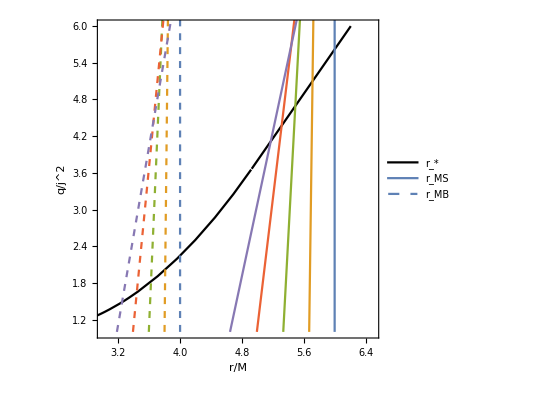

```mathematica
q=x j^2;M=1;
starrms=Show[Plot[qstar,{qr,2,14},PlotRange->{{3,6.5},{1,6}},Frame->True,Axes->False,FrameLabel->{"r/M","q/j^2"},PlotStyle->{Black,Thick},AspectRatio->1,PlotLegends->{Subscript["r","*"]},LabelStyle->Directive[20,FontFamily->"Times New Roman"]],
ParametricPlot[{{rms/.j->0.0,x},{rms/.j->0.1,x},{rms/.j->0.2,x},{rms/.j->0.3,x},{rms/.j->0.4,x}},{x,1,10},PlotStyle->Line,PlotLegends->{Subscript["r","MS"]},LabelStyle->Directive[20,FontFamily->"Times New Roman"]],
ParametricPlot[{{rmb/.j->0.0,x},{rmb/.j->0.1,x},{rmb/.j->0.2,x},{rmb/.j->0.3,x},{rmb/.j->0.4,x}},{x,1,10},PlotStyle->Dashed,PlotLegends->{Subscript["r","MB"]},LabelStyle->Directive[20,FontFamily->"Times New Roman"]]]
Clear[j,q,x,M]
```

```mathematica
startable=Table[{qstar,qr},{qr,2,9,0.1}];
Rstar=Interpolation[startable];
```

```mathematica
star[x_,y_,z_]=x^2+y^2+z^2-rstar^2 ;
```

```mathematica
c= 2.99792458 10^10 ;G=6.67428 10^(-8); Msun=1.98892 10^(33);
rStar[M_,R_]:=R 10^5/(M Msun G/c^2);                                                                                         (* M in Msun, R in km -> R in M *)
a1=1.317;a2=-0.05043;a3=0.04806;a4 =-0.002692;
unij[M_,R_]:= 2*π*freq*M*147600/c*(a1*R+a2*R^2+a3*R^3+a4*R^4);         (* M in Msun, R in M -> j *)
b1=-0.2588;b2=0.2274;b3=0.0009528;b4=-0.0007747;
uniq[R_]:= (b1*R+b2*R^2+b3*R^3+b4*R^4);                                                                          (* R in M -> q/j^2 *)
```

### Plots

```mathematica
j = 0.240288;                                       (*   specific angular momentum of the star   *)
q=0.166010;                                        (*   specific quadrupole moment of the star   *)
rstar=Rstar[q/j^2];Print["R* = ",rstar," M, r_ISCO = ",rms," M"];
ell=l/.h->Pi/2; ell0=l0/.r0->rstar;
Print["r_0 = ",r0=r/.NSolve[ell-ell0==0,r,Reals][[2]]," M, β_max = ",beta/.rin->rstar]
maxtorus[r_,h_]= frin/.rin->rstar;
torus1[r_,h_]=fbeta/.β->0.05;
torus2[r_,h_]=fbeta/.β->0.10;
torus3[r_,h_]=fbeta/.β->0.13;
```

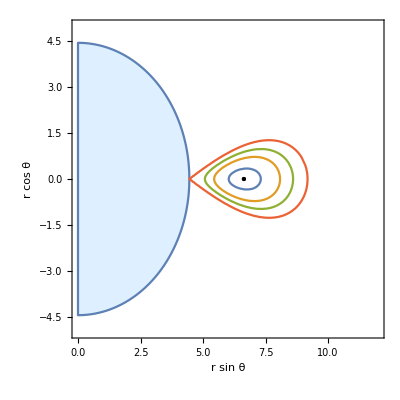

```mathematica
plot1=Show[RegionPlot[x^2+y^2<rstar^2,{x,0,rstar},{y,-rstar,rstar},PlotRange->{{0,12},{-5,5}},PlotStyle->LightBlue,FrameLabel->{"r sin θ","r cos θ"}],
ContourPlot[{torus1[Sqrt[x x+y y],ArcTan[y,x]]==0,torus2[Sqrt[x x+y y],ArcTan[y,x]]==0,torus3[Sqrt[x x+y y],ArcTan[y,x]]==0,maxtorus[Sqrt[x x+y y],ArcTan[y,x]]==0},{x,rstar,15},{y,-5,5}],
ListPlot[{{r0,0}},PlotStyle->{Black,PointSize[Medium]}]]
```

```mathematica
plot2=Show[ContourPlot3D[star[x,y,z]==0,{x,-10,10},{y,-10,10},{z,-10,10},Mesh->None,ContourStyle->LightYellow],
ContourPlot3D[torus2[Sqrt[x*x+y*y+z*z],ArcTan[z,Sqrt[x*x+y*y]]]==0,{x,-10,10},{y,-10,10},{z,-2,2},Mesh->None,RegionFunction->Function[{x,y,z},Sqrt[x*x+y*y+z*z]>5],RegionBoundaryStyle->None,PlotRange->{Automatic,Automatic,{-10,10}}]]
```

-Graphics3D-

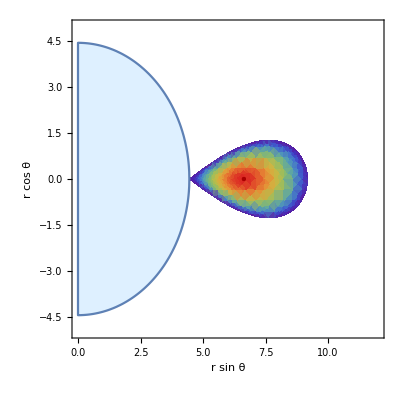

```mathematica
plot3=Show[RegionPlot[x^2+y^2<rstar^2,{x,0,rstar},{y,-rstar,rstar},PlotRange->{{0,12},{-5,5}},PlotStyle->LightBlue,FrameLabel->{"r sin θ","r cos θ"}],
DensityPlot[maxtorus[Sqrt[x x+y y],ArcTan[y,x]],{x,rstar,15},{y,-5,5},RegionFunction->Function[{x,y},maxtorus[Sqrt[x*x+y*y],ArcTan[y,x]]≥0],ColorFunction->"Rainbow"],
ListPlot[{{r0,0}},PlotStyle->{Darker[Red],PointSize[Medium]}]]
```